## Boson Quadratic Hamiltonian

## Calculating the Matrix Elements of H

## H_b=ϵb^+b-v(b^+b^++bb)

### Case |0>,|2>,|4>,...

```mathematica
dif[n_,m_]:=n-m;
matEl02[n_,m_,e_,v_]:=Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat02[n_,e_,v_]:=Table[Table[matEl02[2(j-1),2(i-1),e,v],{i,1,n}],{j,1,n}];
```

```mathematica
Hmat02[6,e,v]//MatrixForm
```

(0 | -√2 v | 0 | 0 | 0 | 0
-√2 v | 2 e | -2 √3 v | 0 | 0 | 0
0 | -2 √3 v | 4 e | -√30 v | 0 | 0
0 | 0 | -√30 v | 6 e | -2 √14 v | 0
0 | 0 | 0 | -2 √14 v | 8 e | -3 √10 v
0 | 0 | 0 | 0 | -3 √10 v | 10 e)

```mathematica
Hmat02[6,e,v]/e//MatrixForm
```

(0 | -(√2 v)/e | 0 | 0 | 0 | 0
-(√2 v)/e | 2 | -(2 √3 v)/e | 0 | 0 | 0
0 | -(2 √3 v)/e | 4 | -(√30 v)/e | 0 | 0
0 | 0 | -(√30 v)/e | 6 | -(2 √14 v)/e | 0
0 | 0 | 0 | -(2 √14 v)/e | 8 | -(3 √10 v)/e
0 | 0 | 0 | 0 | -(3 √10 v)/e | 10)

```mathematica
redM02[n_,q_]:=Hmat02[n,1,q];
```

### Case |1>,|3>,|5>,...

```mathematica
matEl13[n_,m_,e_,v_]:=Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat13[n_,e_,v_]:=Table[Table[matEl13[2j+1,2i+1,e,v],{i,0,n-1}],{j,0,n-1}];
```

```mathematica
Hmat13[6,e,v]//MatrixForm
```

(e | -√6 v | 0 | 0 | 0 | 0
-√6 v | 3 e | -2 √5 v | 0 | 0 | 0
0 | -2 √5 v | 5 e | -√42 v | 0 | 0
0 | 0 | -√42 v | 7 e | -6 √2 v | 0
0 | 0 | 0 | -6 √2 v | 9 e | -√110 v
0 | 0 | 0 | 0 | -√110 v | 11 e)

```mathematica
Hmat13[6,e,v]/e//MatrixForm
```

(1 | -(√6 v)/e | 0 | 0 | 0 | 0
-(√6 v)/e | 3 | -(2 √5 v)/e | 0 | 0 | 0
0 | -(2 √5 v)/e | 5 | -(√42 v)/e | 0 | 0
0 | 0 | -(√42 v)/e | 7 | -(6 √2 v)/e | 0
0 | 0 | 0 | -(6 √2 v)/e | 9 | -(√110 v)/e
0 | 0 | 0 | 0 | -(√110 v)/e | 11)

```mathematica
redM13[n_,q_]:=Hmat13[n,1,q];
```

## Solving the eigenvalue and eigenvector equation

## Case 1

```mathematica
redM02[4,q]//MatrixForm
```

(0 | -√2 q | 0 | 0
-√2 q | 2 | -2 √3 q | 0
0 | -2 √3 q | 4 | -√30 q
0 | 0 | -√30 q | 6)

Calculating the eigenvalues

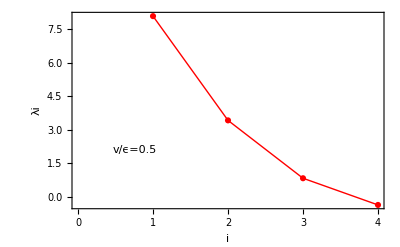

```mathematica
sols02[n_,q_]:=N[Eigenvalues[redM02[n,q]]];
p02[n_,q_]:=ListPlot[sols02[n,q],Axes->False,Frame->True,Joined->True,PlotStyle->{Red,Thick},PlotMarkers->Automatic,PlotRange->Automatic,FrameLabel->{"i","λi"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog -> 
  Inset[Framed[Style[StringTemplate["v/ϵ=``"][q], 20],Background -> None,FrameStyle->White], Scaled[{0.2,0.3}]]];
Show[p02[4,0.5]]
```

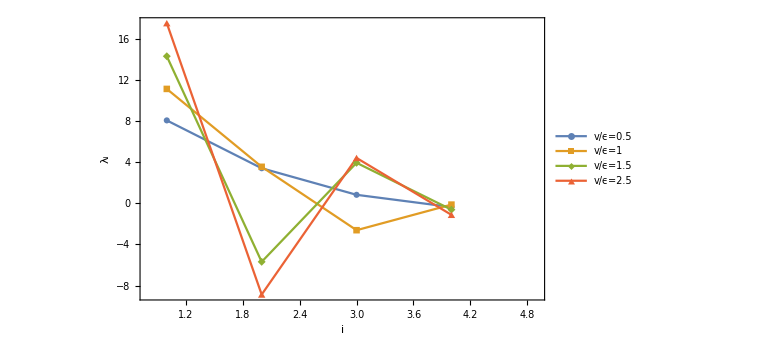

```mathematica
ListPlot[{sols02[4,0.5],sols02[4,1],sols02[4,1.5],sols02[4,2]},Joined->True,Axes->False,Frame->True,PlotMarkers->Automatic,PlotRange->{{0.8,4.9},Automatic},FrameLabel->{"i","λ_i"},LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"v/ϵ=0.5","v/ϵ=1","v/ϵ=1.5","v/ϵ=2.5"},{0.90,0.5}],ImageSize->Large]
```

## Case 2

```mathematica
redM13[4,q]//MatrixForm
```

(1 | -√6 q | 0 | 0
-√6 q | 3 | -2 √5 q | 0
0 | -2 √5 q | 5 | -√42 q
0 | 0 | -√42 q | 7)

Calculating the eigenvalues

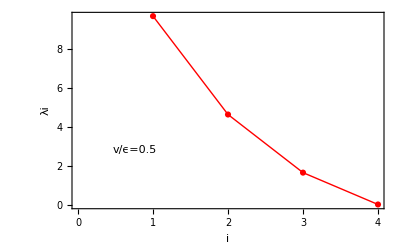

```mathematica
sols13[n_,q_]:=N[Eigenvalues[redM13[n,q]]];
p13[n_,q_]:=ListPlot[sols13[n,q],Axes->False,Frame->True,Joined->True,PlotStyle->{Red,Thick},PlotMarkers->Automatic,PlotRange->Automatic,FrameLabel->{"i","λi"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog -> 
  Inset[Framed[Style[StringTemplate["v/ϵ=``"][q], 20],Background -> None,FrameStyle->White], Scaled[{0.2,0.3}]]];
Show[p13[4,0.5]]
```

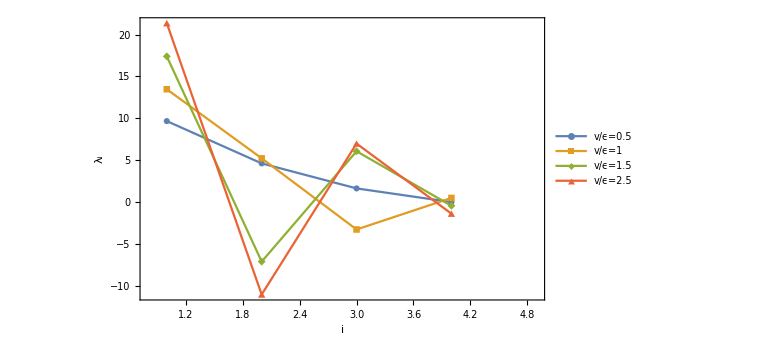

```mathematica
ListPlot[{sols13[4,0.5],sols13[4,1],sols13[4,1.5],sols13[4,2]},Joined->True,Axes->False,Frame->True,PlotMarkers->Automatic,PlotRange->{{0.8,4.9},Automatic},FrameLabel->{"i","λ_i"},LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"v/ϵ=0.5","v/ϵ=1","v/ϵ=1.5","v/ϵ=2.5"},{0.90,0.5}],ImageSize->Large]
```

## Lambdas - evolution with the ratio q

### Case 1: even k-bosonic states

```mathematica
sols02[n_,q_]:=N[Eigenvalues[redM02[n,q]]];
p02[n_,q_]:=ListPlot[sols02[n,q],Axes->False,Frame->True,Joined->True,PlotStyle->{Red,Thick},PlotMarkers->Automatic,PlotRange->Automatic,FrameLabel->{"i","λi"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Framed[Style[StringTemplate["ϵ/v=``"][q],20],Background->None,FrameStyle->White],Scaled[{0.2,0.3}]]];
lambdaId0[n_,id_]:=Table[{q,sols02[n,q][[id]]},{q,0.05,3,0.1}];
```

```mathematica
myplot[n_,id_]:=ListPlot[lambdaId[n,id],Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {Automatic, Automatic}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"},Epilog->Inset[Framed[Style[StringTemplate["i=``"][id],20]],Scaled[{0.15,0.15}]]];
```

### Case 2 : odd k - bosonic states

```mathematica
sols13[n_,q_]:=N[Eigenvalues[redM13[n,q]]];
p13[n_,q_]:=ListPlot[sols13[n,q],Axes->False,Frame->True,Joined->True,PlotStyle->{Red,Thick},PlotMarkers->Automatic,PlotRange->Automatic,FrameLabel->{"i","λi"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Framed[Style[StringTemplate["ϵ/v=``"][q],20],Background->None,FrameStyle->White],Scaled[{0.2,0.3}]]];
lambdaId1[n_,id_]:=Table[{q,sols13[n,q][[id]]},{q,0.05,3,0.1}];
```

```mathematica
lambdaId1[4,1]
```

{{0.05,7.05149},{0.15,7.40961},{0.25,7.96752},{0.35,8.61983},{0.45,9.32072},{0.55,10.0495},{0.65,10.7959},{0.75,11.554},{0.85,12.3204},{0.95,13.0928},{1.05,13.8697},{1.15,14.6502},{1.25,15.4334},{1.35,16.2189},{1.45,17.0062},{1.55,17.7951},{1.65,18.5851},{1.75,19.3763},{1.85,20.1683},{1.95,20.9611},{2.05,21.7546},{2.15,22.5487},{2.25,23.3433},{2.35,24.1384},{2.45,24.9339},{2.55,25.7297},{2.65,26.5259},{2.75,27.3223},{2.85,28.119},{2.95,28.9159}}